```mathematica
(* Load MaTeX *)
<<MaTeX`
fontsize=8;
imagesize=246;
SetOptions[MaTeX,FontSize->fontsize];
SetOptions[Plot,BaseStyle->{FontSize->fontsize, FontFamily->"Times New Roman"}];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"];
cm=72/2.54;
DefaultFrameStyle->Directive[Black,10];
```

```mathematica
(* Some Labels needed for the figures *) 
f5g6=Graphics[Text[MaTeX["\\gamma=6"], {0.9695,2.939}]];
f5g5=Graphics[ Text[MaTeX["\\gamma=5"], {0.9644,2.728}]];
f5g4=Graphics[Text[MaTeX["\\gamma=4"],{0.9557,2.50}]];
f5g3=Graphics[Text[MaTeX["\\gamma=3"],{0.9345,2.235}]];
f5g2=Graphics[Text[MaTeX["\\gamma=2"],{0.8945,1.926}]];
f5g1=Graphics[Text[MaTeX["\\gamma=1"],{0.82,1.55}]];
t0=Graphics[Text[MaTeX["\\tau=1.000"],{0.88,1.92}]];
t01=Graphics[Text[MaTeX["\\tau=1.001"],{0.90,2.20}]];
t05=Graphics[Text[MaTeX["\\tau=1.005"],{0.913,2.90}]];
t10=Graphics[Text[MaTeX["\\tau=1.010"],{0.909,3.33}]];
t15=Graphics[Text[MaTeX["\\tau=1.015"],{0.917,3.89}]];
f1g6=Graphics[Text[MaTeX["\\gamma=6"],{0.98,3.07}]];
f1g5=Graphics[Text[MaTeX["\\gamma=5"],{0.98,2.86}]];
f1g4=Graphics[Text[MaTeX["\\gamma=4"],{0.98,2.63}]];
f1g3=Graphics[Text[MaTeX["\\gamma=3"],{0.98,2.37}]];
f1g2=Graphics[Text[MaTeX["\\gamma=2"],{0.98,2.07}]];
f1g1=Graphics[Text[MaTeX["\\gamma=1"],{0.98,1.68}]];
p1=Graphics[Text[MaTeX["P", FontSize->10],{0.942,2.49}]];
x1=ListPlot[{{0.95,2.5}}, PlotStyle->{PointSize[0.02], Black}, PlotRange->{{0.8,1},{1,3.5}}, AspectRatio->1];
c1=MaTeX["Currency \\ area", FontSize->10];
c2 =MaTeX["Flexible", FontSize->10];
```

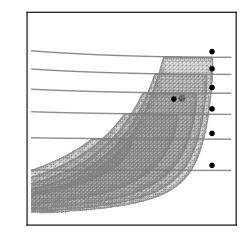

```mathematica
(* FIGURE 1 *)fig1=Show[Show[x1], Show[TPlot1], Show[tpl2],f1g6,f1g5,f1g4,f1g3,f1g2,f1g1,p1,Frame->True,FrameLabel->{MaTeX["z", FontSize->10],MaTeX["\\sigma", FontSize->10]},FrameTicks->{{Transpose[{Range[1.5,3.0,0.5],MaTeX[Range[1.5,3.0,0.5]]}],None},{Transpose[{Range[0.8,1.0,0.05],MaTeX[Range[0.8,1.0,0.05]]}],None}},RotateLabel->False, ImageSize->imagesize]
```

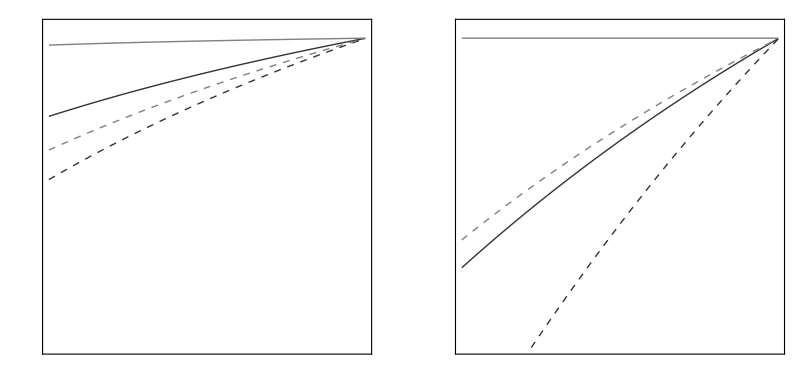

```mathematica
(* FIGURE 2 *)
fig2a=Plot[{
δuc[z,.99,1.5,5,1.00001,1],
δuf[z,.99,1.5,5,1.00001,1],
δdc[z,.99,1.5,5,1.00001,1],
δdf[z,.99,1.5,5,1.00001,1]},
{z,0.6,.999},
 PlotStyle->{{Thick,GrayLevel[0.2]},{Thin,GrayLevel[0.5]},{Thick,Dashed,GrayLevel[0.2]},{Thin,Dashed,GrayLevel[0.5]}},
PlotRange->{0.75,1.01},
Frame->True,
FrameTicks->{{Transpose[{Range[0.8,1.0,0.05],MaTeX[Range[0.8,1.0,0.05]]}],None},{Transpose[{Range[0.6,1.0,0.1],MaTeX[Range[0.6,1.0,0.1]]}],None}},
FrameLabel->{
MaTeX["z", FontSize->10],
MaTeX["\\delta", FontSize->10]
},
RotateLabel->False,
PlotLegends->Placed[MaTeX[{"\\bar{\\delta}^c","\\bar{\\delta}^f", "\\underline{\\delta}^c", "\\underline{\\delta}^f"},Magnification->1],{0.85, 0.32}],
ImageSize->0.95*imagesize
];

fig2b=Plot[{
δuc[z,.99,2.5,5,1.00001,1],
δuf[z,.99,2.5,5,1.00001,1],
δdc[z,.99,2.5,5,1.00001,1],
δdf[z,.99,2.5,5,1.00001,1]},
{z,0.6,.999},
 PlotStyle->{{Thick,GrayLevel[0.2]},{Thin,GrayLevel[0.5]},{Thick,Dashed,GrayLevel[0.2]},{Thin,Dashed,GrayLevel[0.5]}},
PlotRange->{0.75,1.01},
Frame->True,
FrameTicks->{{Transpose[{Range[0.8,1.0,0.05],MaTeX[Range[0.8,1.0,0.05]]}],None},{Transpose[{Range[0.6,1.0,0.1],MaTeX[Range[0.6,1.0,0.1]]}],None}},
FrameLabel->{
MaTeX["z", FontSize->10],
MaTeX["\\delta", FontSize->10]
},
RotateLabel->False,
PlotLegends->Placed[MaTeX[{"\\bar{\\delta}^c","\\bar{\\delta}^f", "\\underline{\\delta}^c", "\\underline{\\delta}^f"},Magnification->1],{0.85, 0.32}],
ImageSize->0.95*imagesize
];
GraphicsGrid[{{fig2a, fig2b}}]
```

-Graphics-

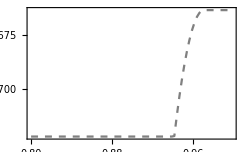

-Graphics-

```mathematica
(* FIGURE 3 *)fig3a=Plot[{Callout[EUCf[0.9,δ,0.99,2.,5,5.,1.],Magnify[c2,1], {0.875,Below},0.875],Callout[EUCc[0.9,δ,0.99,2.,5,5.,1.],Magnify[c1, 1],{0.925,Above},0.925]},{δ,0.8,.999},PlotStyle->{{GrayLevel[0.5],Thick},{GrayLevel[0.2], Thick}},PlotRange->Full, Frame->True,FrameLabel->{MaTeX["\\delta", FontSize->10],MaTeX["\\mathbb{E}_s[U^r_s]", FontSize->10]},FrameTicks->{{None, None},{Transpose[{Range[0.8,1.0,0.05],MaTeX[Range[0.8,1.0,0.05]]}],None}},RotateLabel->False, PlotRange->All, ImageSize->imagesize];
fig3b=Show[PlotEUCFBbw,Frame->True,PlotRange->All, ImageSize-> imagesize];

fig3=Show[fig3a,fig3b]
```

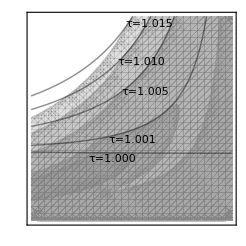

```mathematica
(* FIGURE 4 *)fig4=Show[lplots,TPlot2,t0,t01,t05,t10,t15,FrameLabel->{MaTeX["z", FontSize->10],MaTeX["\\sigma", FontSize->10]},FrameTicks->{{Transpose[{Range[1.0,4.0,0.5],MaTeX[Range[1.0,4.0,0.5]]}],None},{Transpose[{Range[0.8,1.0,0.05],MaTeX[Range[0.8,1.0,0.05]]}],None}},RotateLabel->False, ImageSize->imagesize]
```

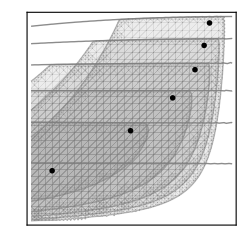

```mathematica
(* FIGURE 5 *)fig5=Show[pty, ptx,f5g6,f5g5,f5g4,f5g3,f5g2,f5g1, Frame->True,FrameTicks->{{Transpose[{Range[1.5,3.0,0.5],MaTeX[Range[1.5,3.0,0.5]]}],None},{Transpose[{Range[0.8,1.0,0.05],MaTeX[Range[0.8,1.0,0.05]]}],None}},FrameLabel->{MaTeX["z",  FontSize->10],MaTeX["\\sigma",  FontSize->10]},FrameTicksStyle->Directive[Black,10],PlotRange->All,RotateLabel->False,ImageSize->imagesize
]
```

```mathematica
(* Export Figures to PDF and EPS Formats *)
Export[NotebookDirectory[]<>"Fig1.pdf",fig1] 
 Export[NotebookDirectory[]<>"Fig1.eps",fig1] 
 Export[NotebookDirectory[]<>"Fig2a.pdf",fig2a]
Export[NotebookDirectory[]<>"Fig2b.pdf",fig2b]
 Export[NotebookDirectory[]<>"Fig2a.eps",fig2a]
Export[NotebookDirectory[]<>"Fig2b.eps",fig2b]
 Export[NotebookDirectory[]<>"Fig3.pdf",fig3] 
 Export[NotebookDirectory[]<>"Fig3.eps",fig3]
 Export[NotebookDirectory[]<>"Fig4.pdf",fig4] 
 Export[NotebookDirectory[]<>"Fig4.eps",fig4]  
 Export[NotebookDirectory[]<>"Fig5.pdf",fig5] 
 Export[NotebookDirectory[]<>"Fig5.eps",fig5]
```